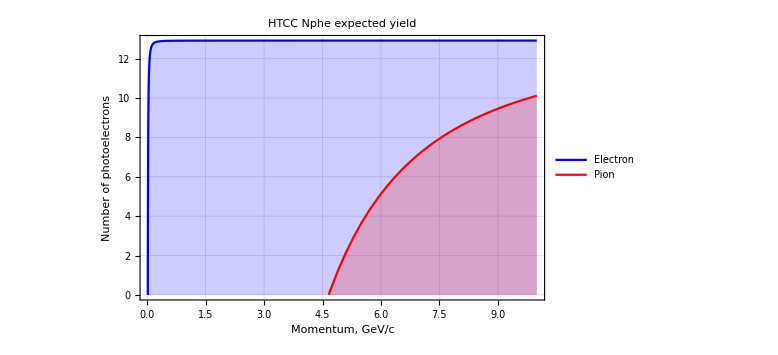

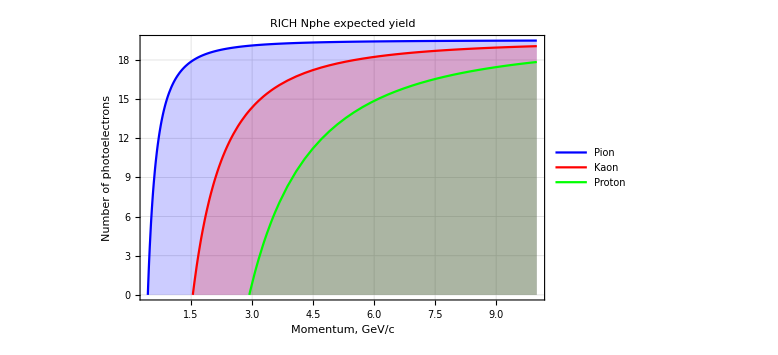

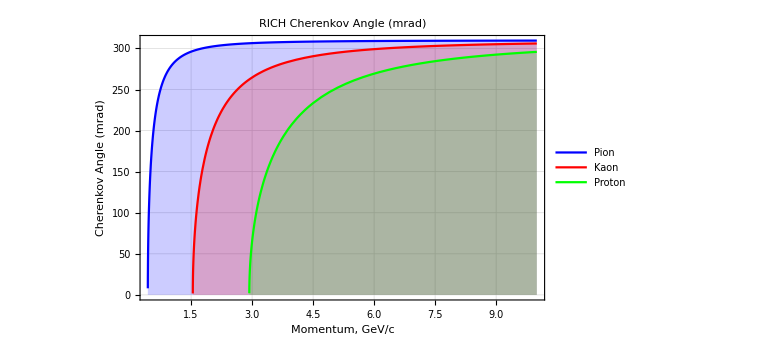

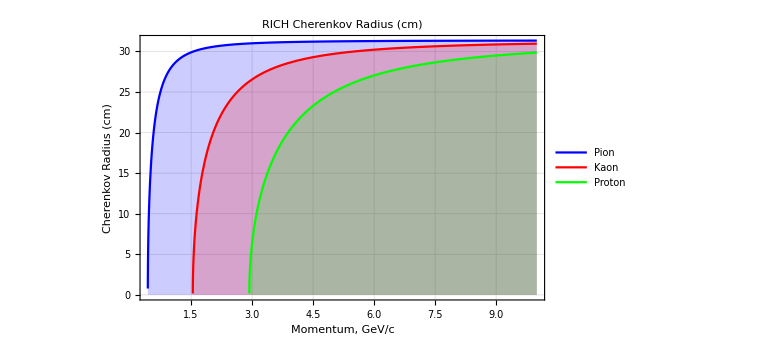

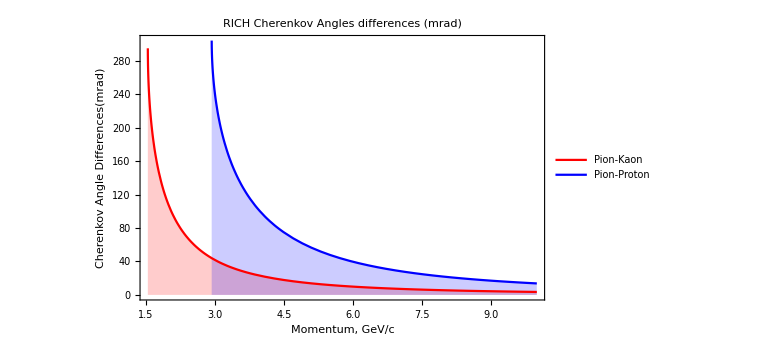

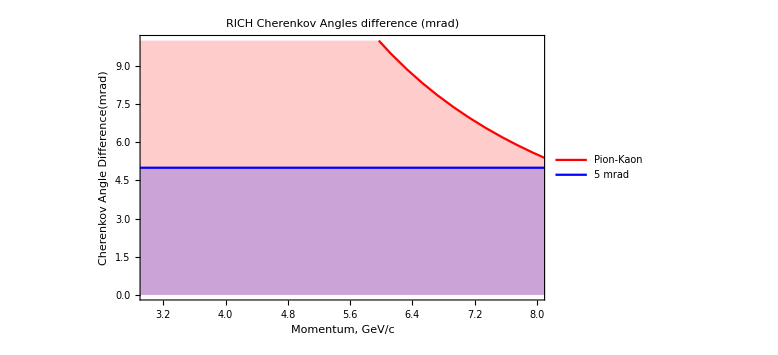

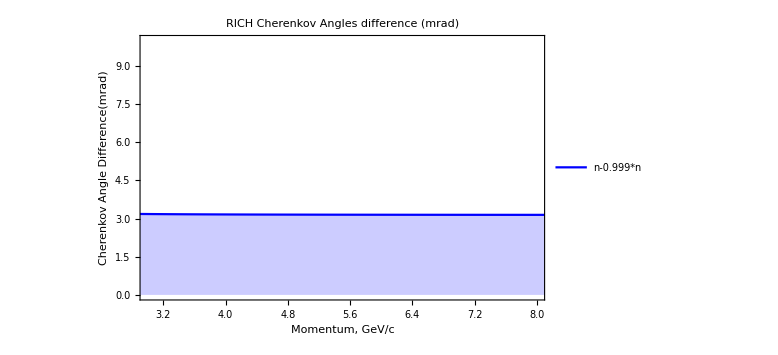

```mathematica
me        = 0.00051099907 ;
mmu      = 0.1056583745 ;
mpi0    = 0.1349764 ;
mpi       = 0.13956995 ;
mk0       = 0.497672 ;
mk         = 0.493677 ;
meta      = 0.547853 ;
mrho      = 0.77549 ;
mom         = 0.78265 ;
metap     = 0.95778 ;
mphi       = 1.01945 ;
mf1         = 1.2821 ;
ma2         = 1.3183;
mn           = 0.93956563 ;
mp           = 0.93827231 ;

nco2=1.00044892;
nc4f10=1.00134;
nneon=1.000066102;
naero=1.05;
Laero=2;
Lpmt=98;

fom=105;
n=naero;
pmax=10;
beta[m_,p_]                :=p/Sqrt[p^2+m^2];
cosCh[m_,p_,n_]     :=1./(n*beta[m,p]);
AngleCh[m_,p_,n_]:=ArcCos[cosCh[m,p,n]];
RCh[m_,p_,n_]         :=Lpmt*Sqrt[1.-cosCh[m,p,n]^2]/cosCh[m,p,n];
Chmrad[m_,p_,n_]  :=1000*ArcCos[cosCh[m,p,n]];
Nphe[m_,p_,n_,l_,fom_]:=Laero*fom*Sin[AngleCh[m,p,n]]^2;
NpheHTCC[m_,p_,l_,fom_]:=l*fom*Sin[AngleCh[m,p,nco2]]^2;
l=100.;
fomHTCC=120.;
lHTCC=120.;
Plot[{NpheHTCC[me,p,lHTCC,fomHTCC],NpheHTCC[mpi,p,lHTCC,fomHTCC]},
{p,0,pmax},PlotRange->{{0,pmax},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Number of photoelectrons"},
PlotLabel->"HTCC Nphe expected yield",
PlotLegends->Placed[{"Electron","Pion"},Center],
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Red,Green,Yellow},
GridLines->Automatic,
ImageSize->Large]

Plot[{Nphe[mpi,p,n,l,fom],Nphe[mk,p,n,l,fom],Nphe[mp,p,n,l,fom]},{p,0,pmax},PlotRange->{{0,pmax},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Number of photoelectrons"},
PlotLabel->"RICH Nphe expected yield",
PlotLegends->Placed[{"Pion","Kaon","Proton"},Center],
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Red,Green,Yellow},
GridLines->Automatic,
ImageSize->Large]

Plot[{Chmrad[mpi,p,n],Chmrad[mk,p,n],Chmrad[mp,p,n]},{p,0,pmax},PlotRange->{{0,pmax},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle (mrad)"},
PlotLabel->"RICH Cherenkov Angle (mrad)",
PlotLegends->Placed[{"Pion","Kaon","Proton"},Center],
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Red,Green},
GridLines->Automatic,
ImageSize->Large]

Plot[{RCh[mpi,p,n],RCh[mk,p,n],RCh[mp,p,n]},{p,0,pmax},PlotRange->{{0,pmax},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Radius (cm)"},
PlotLabel->"RICH Cherenkov Radius (cm)",
PlotLegends->Placed[{"Pion","Kaon","Proton"},Center],
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Red,Green},
GridLines->Automatic,
ImageSize->Large]

Plot[{Chmrad[mpi,p,n]-Chmrad[mk,p,n],Chmrad[mpi,p,n]-Chmrad[mp,p,n]},{p,0,pmax},PlotRange->{{3,8},{0,All}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle Differences(mrad)"},
PlotLabel->"RICH Cherenkov Angles differences (mrad)",
PlotLegends->Placed[{"Pion-Kaon","Pion-Proton"},Center],
Filling->Axis,
PlotStyle->{Red,Blue,Green},
ImageSize->Large]

Plot[{Chmrad[mpi,p,n]-Chmrad[mk,p,n],5},{p,0,pmax},PlotRange->{{3,8},{0,10}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle Difference(mrad)"},
PlotLabel->"RICH Cherenkov Angles difference (mrad)",
PlotLegends->Placed[{"Pion-Kaon","5 mrad"},Center],
Filling->Axis,
PlotStyle->{Red,Blue},
ImageSize->Large]

Plot[{Chmrad[mpi,p,n]-Chmrad[mpi,p,n*0.999]},{p,0,pmax},PlotRange->{{3,8},{0,10}},
Frame->True,
FrameLabel->{"Momentum, GeV/c","Cherenkov Angle Difference(mrad)"},
PlotLabel->"RICH Cherenkov Angles difference (mrad)",
PlotLegends->Placed[{"n-0.999*n"},Center],
Filling->Axis,
PlotStyle->{Red,Blue},
ImageSize->Large]
```

```mathematica
ll=100; R=ll*Tan[0.3];
a1=ArcTan[R/ll]
a2=ArcTan[R/(ll+0.5)]
a1-a2
a3=ArcTan[(R+0.5)/ll]
a3-a1
2/Sqrt[12.]
```

0.3

0.298595

0.00140519

0.304557

0.00455687

0.57735

```mathematica
30.93362496096232
```